```mathematica
ClearAll[ "Global`*" ];
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Separate elements that are even:

```mathematica
SelectDiscard[{1,2,4,7,6,2},EvenQ]
```

{{2,4,6,2},{1,7}}

Use a pure function to test each element:

```mathematica
SelectDiscard[{1,2,4,7,6,2},#>2&]
```

{{4,7,6},{1,2,2}}

Select only the first expression that satisfies the condition:

```mathematica
SelectDiscard[{1,2,4,7,6,2},#>2&,1]
```

{{4},{7,6,1,2,2}}

Use the operator form of SelectDiscard:

```mathematica
SelectDiscard[EvenQ][{1,2,4,7,6,2}]
```

{{2,4,6,2},{1,7}}

SelectDiscard operates on values in an Associationpaclet:ref/Association:

```mathematica
SelectDiscard[<|a->1,b->2,c->3,d->4|>,#>2&]
```

{<|c→3,d→4|>,<|a→1,b→2|>}

### Scope

SelectDiscard gives elements for which applying the criterion explicitly yields Truepaclet:ref/True in the first list and everything else in the second:

```mathematica
SelectDiscard[{1,2,4,7,x},#>2&]
```

{{4,7},{1,2,x}}

Applying the criterion to the symbolic object x does not explicitly yield Truepaclet:ref/True:

```mathematica
x>2
```

x>2

Find pairs containing x:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,x]&]
```

{{{2,x},{3,x},{5,x}},{{1,y},{4,z}}}

Find up to 2 pairs containing x:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,x]&,2]
```

{{{2,x},{3,x}},{{5,x},{1,y},{4,z}}}

Fewer than the requested elements may be returned:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,z]&,2]
```

{{{4,z}},{{1,y},{2,x},{3,x},{5,x}}}

Use an operator form as selection criterion:

```mathematica
SelectDiscard[Range[10],GreaterThan[3]]
```

{{4,5,6,7,8,9,10},{1,2,3}}

Use SelectDiscard in operator form:

```mathematica
Range[10]//SelectDiscard[GreaterThan[3]]
```

{{4,5,6,7,8,9,10},{1,2,3}}

Separate arguments in Unevaluated code:

```mathematica
SelectDiscard[Unevaluated[1+2+3+4+5],OddQ]
```

{9,6}

### Generalizations & Extensions

SelectDiscard works with any head, not just Listpaclet:ref/List:

```mathematica
SelectDiscard[f[1,a,2,b,3],IntegerQ]
```

{f[1,2,3],f[a,b]}

SelectDiscard works with SparseArraypaclet:ref/SparseArray objects:

```mathematica
s=SparseArray[Table[2^i->i,{i,0,5}]]
```

SparseArray[…]

```mathematica
SelectDiscard[s,EvenQ]
```

{SparseArray[…],{1,3,5}}

The result includes a list since only one can be sparse:

```mathematica
SelectDiscard[s,OddQ]
```

{{1,3,5},SparseArray[…]}

Compare to Select:

```mathematica
Select[s,EvenQ]
```

SparseArray[…]

```mathematica
Select[s,OddQ]
```

{1,3,5}

Separate a Dataset:

```mathematica
dataset=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z","c"->{}|>}]
```

-Graphics-

```mathematica
SelectDiscard[dataset,OddQ[#a]&]
```

-Graphics-

Separate a Graph by testing its vertices:

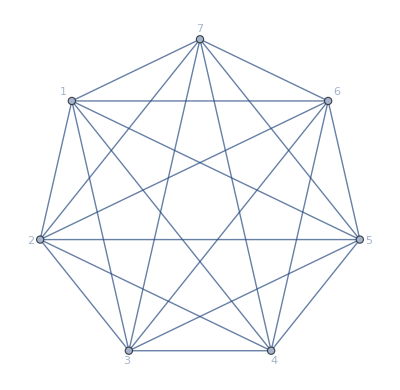
```mathematica
SelectDiscard[-Graphics-,OddQ]
```

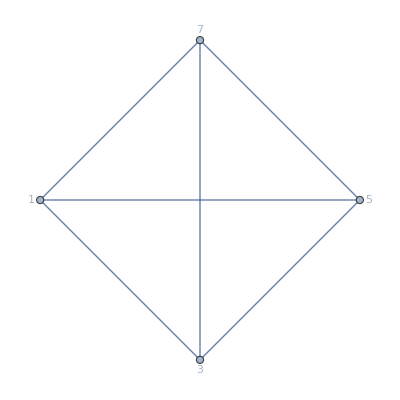
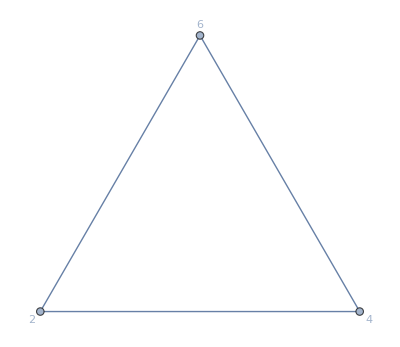

Maybe support this for images? It's kind of weird and arbitrary.

```mathematica
selDiscardImage[img_Image,func_]:=
Module[{mask1,mask2,i1,i2},
mask1=ImageApply[Boole@*TrueQ@*func,img];
mask2=ColorNegate@mask1;
i1=SetAlphaChannel[ImageMultiply[img,mask1],mask1];
i2=SetAlphaChannel[ImageMultiply[img,mask2],mask2];
{i1,i2}
];
```

```mathematica
selDiscardImage[-Graphics-,EuclideanDistance[#,{0,1,0}]<0.8&]
```

{-Graphics-,-Graphics-}

### Applications

Select numbers up to 100 that equal 1 modulo both 3 and 5:

```mathematica
SelectDiscard[Range[100],Mod[#,3]==1&&Mod[#,5]==1&]
```

{{1,16,31,46,61,76,91},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,95,96,97,98,99,100}}

Select 4-tuples that read the same in reverse:

```mathematica
SelectDiscard[Tuples[{a,b},4],#==Reverse[#]&]
```

{{{a,a,a,a},{a,b,b,a},{b,a,a,b},{b,b,b,b}},{{a,a,a,b},{a,a,b,a},{a,a,b,b},{a,b,a,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,a,b,b},{b,b,a,a},{b,b,a,b},{b,b,b,a}}}

Select eigenvalues that lie within the unit circle:

```mathematica
SelectDiscard[Eigenvalues[RandomReal[1,{5,5}]],Abs[#]<1&]
```

{{0.507777+0.223889 ⅈ,0.507777-0.223889 ⅈ,-0.527869+0. ⅈ,-0.104087+0. ⅈ},{2.63854+0. ⅈ}}

Separate built-in Wolfram Language symbols based on whether their names contain less than 10 characters:

```mathematica
{short,long}=SelectDiscard[Names["System`*"],StringLength[#]<10&];
```

```mathematica
short//Short
```

{a,b,c,d,e,f,«1750»,$TraceOn,$Urgent,$Username,$UserName,$Version,\[SystemsModelDelay]}

```mathematica
long//Short
```

{AASTriangle,AbelianGroup,AbortKernels,«5745»,$WolframID,$WolframUUID}

Select numeric quantities from a product:

```mathematica
SelectDiscard[7 π^2 x^2 y^2,NumericQ]
```

{7 π^2,x^2 y^2}

### Properties & Relations

The lengths of list_1 and list_2 will always sum to the length of the original list:

```mathematica
SelectDiscard[Range[10],PrimeQ]
```

{{2,3,5,7},{1,4,6,8,9,10}}

When specifying a maximum, the second list can contain elements that satisfy the given condition:

```mathematica
SelectDiscard[Range[10],PrimeQ,2]
```

{{2,3},{5,7,1,4,6,8,9,10}}

SelectDiscard is similar to TakeDrop except it takes/drops elements using the given function:

```mathematica
list=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
SelectDiscard[list,LessEqualThan[4]]
```

{{1,2,3,4},{5,6,7,8,9,10}}

```mathematica
TakeDrop[list,4]
```

{{1,2,3,4},{5,6,7,8,9,10}}

For crit that always return True or False, SelectDiscard is very similar to GatherBy:

```mathematica
SelectDiscard[Range[10],OddQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

```mathematica
GatherBy[Range[10],OddQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

However, the first list returned by SelectDiscard always corresponds to elements e_i where crit[e_i] gives True:

```mathematica
SelectDiscard[Range[10],EvenQ]
```

{{2,4,6,8,10},{1,3,5,7,9}}

```mathematica
GatherBy[Range[10],EvenQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

Similar results can be obtained with GroupBy:

```mathematica
Lookup[GroupBy[Range[10],PrimeQ],{True,False},{}]
```

{{2,3,5,7},{1,4,6,8,9,10}}

However, SelectDiscard works on expressions with any head:

```mathematica
SelectDiscard[g[1,2,4,7,8],#>2&]
```

{g[4,7,8],g[1,2]}

GroupBy does not:

```mathematica
GroupBy[g[1,2,4,7,8],#>2&]
```

GroupBy::list1: The argument g[1,2,4,7,8] is not a valid list of Associations or rules or lists of rules.

GroupBy[g[1,2,4,7,8],#1>2&]

SelectDiscard always gives two lists:

```mathematica
SelectDiscard[{1,2,4,7,x,y},#>2&]
```

{{4,7},{1,2,x,y}}

```mathematica
SelectDiscard[Range[5],IntegerQ]
```

{{1,2,3,4,5},{}}

Compare with GatherBy and GroupBy:

```mathematica
GatherBy[{1,2,4,7,x,y},#>2&]
```

{{1,2},{4,7},{x},{y}}

```mathematica
GroupBy[{1,2,4,7,x,y},#>2&]
```

<|False→{1,2},True→{4,7},x>2→{x},y>2→{y}|>

```mathematica
GroupBy[Range[5],IntegerQ]
```

<|True→{1,2,3,4,5}|>

```mathematica
GatherBy[Range[5],IntegerQ]
```

{{1,2,3,4,5}}

Similar results can be obtained with a combination of Select and DeleteElements:

```mathematica
list={1,2,2,3,3,4};
```

```mathematica
SelectDiscard[list,EvenQ]
```

{{2,2,4},{1,3,3}}

```mathematica
With[{sel=Select[list,EvenQ]},{sel,DeleteElements[list,sel]}]
```

{{2,2,4},{1,3,3}}

SelectDiscard tends to perform better with large lists:

```mathematica
list=RandomInteger[100,10000];
```

```mathematica
First[RepeatedTiming[SelectDiscard[list,EvenQ]]]
```

0.00613686

```mathematica
First[RepeatedTiming[With[{sel=Select[list,EvenQ]},{sel,DeleteElements[list,sel]}]]]
```

0.400921

The first list returned by SelectDiscard[list,crit] is equivalent to what's returned by Select[list,crit]:

```mathematica
list={-2,0,1,3,3,x,y};
```

```mathematica
First[SelectDiscard[list,Positive]]===Select[list,Positive]
```

True

The second list is effectively equivalent to Select[list,Not@*TrueQ@*crit]:

```mathematica
Last[SelectDiscard[list,Positive]]===Select[list,Not@*TrueQ@*Positive]
```

True

### Possible Issues

When specifying a limit, the second list can contain elements e_i where crit[e_i] is True:

```mathematica
SelectDiscard[{1,2,4,7,6,2},EvenQ,2]
```

{{2,4},{6,2,1,7}}